```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
NotebookDirectory[]
Needs["plots`"];
SetOptions[Plot, Frame->True, Axes->False, FrameStyle->Thick, ImageSize->8*72, LabelStyle->{FontSize->25}];
SetOptions[ArrayPlot, Frame->True, Axes->False, FrameStyle->Thick, ImageSize->8*72, LabelStyle->{FontSize->25}];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma/

Needs::nocont: Context "plots`" was not created when Needs was evaluated.

## Sec 3

```mathematica
(* Make a map of the DEEP2 mask *)
```

```mathematica
deep2 = Import["../data/deep2/windowf.31.fits","RawData"];
deep2meta = Import["../data/deep2/windowf.31.fits","Metadata"];
deep2 = Flatten[deep2, {{1,2},{3}}];
limits = ({{"RALIM0", "DECLIM0"}, {"RALIM1", "DECLIM1"}}/. deep2meta)[[All,All,1]];
ndim = ({"NRA","NDEC"}/.deep2meta)[[All,1]];
dlim = (limits[[2]] - limits[[1]])/ndim;
```

```mathematica
p1 = ArrayPlot[deep2, Frame->True, ImageMargins->0, DataRange->Transpose[limits], FrameTicks->{{{-0.1,0.0,0.1,0.2,0.3},None},{{351.4,351.6,351.8,352.0} ,None}}]
```

-Graphics-

```mathematica
p2 = Plot[None, {x, limits[[1,1]], limits[[2,1]]}, PlotRange->Transpose[limits], Epilog->Inset[p1,limits[[1]], {0,0}, Automatic], FrameLabel->{"RA","Dec"}, ImageMargins->20, FrameTicks->{{351.4,351.6,351.8,352.0}, Automatic, None, None}, ImageSize->10*72]
```

-Graphics-

```mathematica
(*Export["../tex/plots/deep2mask.pdf", p2]*)
```

../tex/plots/deep2mask.pdf

```mathematica
Clear[deep2, deep2meta, limits, ndim, dlim, p1, p2];
```

## Scratch

```mathematica
tmp = readSims["../data/deep2/rrdump_04_16384000.dat"];
```

```mathematica
Dimensions[tmp]
```

{100}

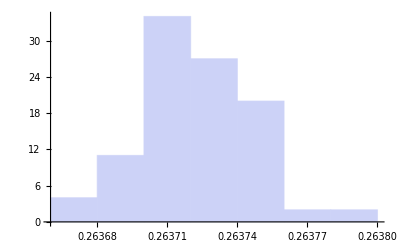

```mathematica
Histogram[tmp]
```

```mathematica
stats[readSims["../data/deep2/rrdump_04_16384000.dat"]]
```

{0.263722,0.0000240764}

```mathematica
"ddd"<>ToString[NumberForm[1234, 10, NumberPadding->{"0","0"}]]
```

ddd00000001234

```mathematica
genfilenames["../data/deep2/rrdump", 4, 1000]
```

../data/deep2/rrdump_04_00001000.dat